```mathematica
<<MultiAgent`

mas = ({1, #}&/@Range[4])
getMarketNumber[#[[1]],#[[2]]] &/@ mas
getMarketNumber[5,1]
f[arg_] := If[arg>0,arg,0];
f/@RandomVariate[CrProduce,productsN]
```

{{1,1},{1,2},{1,3},{1,4}}

Last::normal: Nonatomic expression expected at position 1 in Last[marketsNums].

{$Failed,1,2,3}

4

RandomVariate::unsdst: The first argument CrProduce is not a valid distribution.

RandomVariate::array: The array dimensions If[productsN > 0, productsN, 0] given in position 2 of RandomVariate[If[CrProduce > 0, CrProduce, 0], If[productsN > 0, productsN, 0]] should be a list of non-negative machine-sized integers giving the dimensions for the result.

RandomVariate[If[CrProduce>0,CrProduce,0],If[productsN>0,productsN,0]]

```mathematica
(*RemoveGlobal[]*)
```

```mathematica
freeAgents[]

param[1, rProduce]
```

freeAgents[]

param[1,rProduce]

```mathematica
param[1,rProduce]
```

param[1,rProduce]

```mathematica
{
ag=createAgent[{Produce,Hold@strProduceResource[AgentNUM,"Ferrum",2]},{Produce,Hold@strProduceResource[AgentNUM,"Gold",1]}];
addAgent[ag]
```

{a$1,a$2}

```mathematica
MultiAgent`Private`agents[a$1];
```

```mathematica
Binary[arr_]:=arr/.x_/;(x≠0)->1;

Binary@{1,5.5, -2, 0, 0.1,2}
```

{1,1,1,0,1,1}

```mathematica
===
 ___
~
```

```mathematica
/@
//
# &
?
/. ->
<<
/;
==
:
@@
{}
;;
_
! &@
Switch
Module
Sequence
MapThread
OptionValue
Hold
Break
Rest
Release
Protect
->
#[[;;l]]
```

```mathematica
x=2
```

2

```mathematica
v = {1,2,3}
```

{1,2,3}

```mathematica
N[v/(v+1)]
```

{0.5,0.666667,0.75}

```mathematica
Exp[%]
```

{1.64872,1.94773,2.117}

```mathematica
E^0.5
```

1.64872

```mathematica
Clear@f
```

```mathematica
?f
```

Global`f

```mathematica
f//Clear
```

```mathematica
f[x_]:=x^2+34;
```

```mathematica
?f
```

Global`f

f[x_]:=x^2+34

```mathematica
f//Clear
```

```mathematica
?f
```

Global`f

```mathematica
products
```

{1,2,3}

```mathematica
DownValues[param]
```

{HoldPattern[param[1,MultiAgent`Private`kConsume]]:>0.457415,HoldPattern[param[1,MultiAgent`Private`kProduce]]:>{{0,3,5/2,0},{0,0,0,0},{0,0,0,0},{0,1/12,0,0}},HoldPattern[param[1,MultiAgent`Private`rConsume]]:>{9.59467,0,1.84197,1.70354},HoldPattern[param[1,MultiAgent`Private`rProduce]]:>{1.0339,0,0,0},HoldPattern[param[2,MultiAgent`Private`kConsume]]:>0.773052,HoldPattern[param[2,MultiAgent`Private`kProduce]]:>{{0,3,0,0},{1/12,0,3,3},{0,1/12,0,0},{0,0,0,0}},HoldPattern[param[2,MultiAgent`Private`rConsume]]:>{0,4.51418,4.98475,1.89156},HoldPattern[param[2,MultiAgent`Private`rProduce]]:>{0,1.0742,0,0},HoldPattern[param[3,MultiAgent`Private`kConsume]]:>0.830063,HoldPattern[param[3,MultiAgent`Private`kProduce]]:>{{0,0,0,0},{1/12,0,0,3},{1/10,1/12,0,0},{0,0,0,0}},HoldPattern[param[3,MultiAgent`Private`rConsume]]:>{0,2.22094,2.36637,6.40385},HoldPattern[param[3,MultiAgent`Private`rProduce]]:>{1.7629,0,0.87067,0},HoldPattern[param[4,MultiAgent`Private`kConsume]]:>0.998027,HoldPattern[param[4,MultiAgent`Private`kProduce]]:>{{0,3,0,5/2},{1/12,0,3,3},{1/10,1/12,0,0},{0,0,0,0}},HoldPattern[param[4,MultiAgent`Private`rConsume]]:>{3.2518,3.11036,5.22985,0.686437},HoldPattern[param[4,MultiAgent`Private`rProduce]]:>{0,0,0,0},HoldPattern[param[5,MultiAgent`Private`kConsume]]:>0.653091,HoldPattern[param[5,MultiAgent`Private`kProduce]]:>{{0,0,0,5/2},{1/12,0,0,0},{1/10,1/12,0,0},{0,1/12,0,0}},HoldPattern[param[5,MultiAgent`Private`rConsume]]:>{0.91273,2.27966,1.67725,0},HoldPattern[param[5,MultiAgent`Private`rProduce]]:>{0,1.92445,0,0.712191},HoldPattern[param[6,MultiAgent`Private`kConsume]]:>0.994663,HoldPattern[param[6,MultiAgent`Private`kProduce]]:>{{0,0,0,0},{0,0,0,3},{1/10,0,0,0},{1/10,0,0,0}},HoldPattern[param[6,MultiAgent`Private`rConsume]]:>{4.16925,6.39515,2.21212,2.65977},HoldPattern[param[6,MultiAgent`Private`rProduce]]:>{0,0,0,0.412126},HoldPattern[param[7,MultiAgent`Private`kConsume]]:>0.625537,HoldPattern[param[7,MultiAgent`Private`kProduce]]:>{{0,3,5/2,5/2},{0,0,0,0},{1/10,0,0,0},{1/10,1/12,0,0}},HoldPattern[param[7,MultiAgent`Private`rConsume]]:>{0,4.04088,3.39167,8.81269},HoldPattern[param[7,MultiAgent`Private`rProduce]]:>{0,1.21894,0,0.0734686},HoldPattern[param[8,MultiAgent`Private`kConsume]]:>0.946472,HoldPattern[param[8,MultiAgent`Private`kProduce]]:>{{0,0,0,0},{0,0,0,0},{1/10,1/12,0,0},{1/10,0,0,0}},HoldPattern[param[8,MultiAgent`Private`rConsume]]:>{4.00127,6.14077,4.8021,4.50075},HoldPattern[param[8,MultiAgent`Private`rProduce]]:>{0,0,0.561211,1.27917},HoldPattern[param[9,MultiAgent`Private`kConsume]]:>0.536126,HoldPattern[param[9,MultiAgent`Private`kProduce]]:>{{0,0,5/2,5/2},{0,0,3,0},{0,0,0,0},{0,0,0,0}},HoldPattern[param[9,MultiAgent`Private`rConsume]]:>{5.85415,1.78034,0,2.63521},HoldPattern[param[9,MultiAgent`Private`rProduce]]:>{2.1989,0,0,0},HoldPattern[param[10,MultiAgent`Private`kConsume]]:>0.42133,HoldPattern[param[10,MultiAgent`Private`kProduce]]:>{{0,3,5/2,5/2},{0,0,3,3},{1/10,0,0,0},{1/10,1/12,0,0}},HoldPattern[param[10,MultiAgent`Private`rConsume]]:>{1.75286,2.15393,1.39858,9.63284},HoldPattern[param[10,MultiAgent`Private`rProduce]]:>{4.95922,2.73647,0,0}}

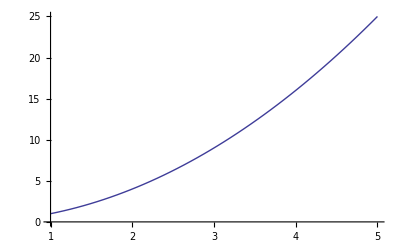

```mathematica
Plot[x^2,{x,1,5}]
```

```mathematica
Options[Plot][[All,All]]
```

{AlignmentPoint→Center,AspectRatio→1/GoldenRatio,Axes→True,AxesLabel→None,AxesOrigin→Automatic,AxesStyle→{},Background→None,BaselinePosition→Automatic,BaseStyle→{},ClippingStyle→None,ColorFunction→Automatic,ColorFunctionScaling→True,ColorOutput→Automatic,ContentSelectable→Automatic,CoordinatesToolOptions→Automatic,DisplayFunction:>$DisplayFunction,Epilog→{},Evaluated→Automatic,EvaluationMonitor→None,Exclusions→Automatic,ExclusionsStyle→None,Filling→None,FillingStyle→Automatic,FormatType:>TraditionalForm,Frame→False,FrameLabel→None,FrameStyle→{},FrameTicks→Automatic,FrameTicksStyle→{},GridLines→None,GridLinesStyle→{},ImageMargins→0.,ImagePadding→All,ImageSize→Automatic,ImageSizeRaw→Automatic,LabelStyle→{},MaxRecursion→Automatic,Mesh→None,MeshFunctions→{#1&},MeshShading→None,MeshStyle→Automatic,Method→Automatic,PerformanceGoal:>$PerformanceGoal,PlotLabel→None,PlotPoints→Automatic,PlotRange→{Full,Automatic},PlotRangeClipping→True,PlotRangePadding→Automatic,PlotRegion→Automatic,PlotStyle→Automatic,PreserveImageOptions→Automatic,Prolog→{},RegionFunction→(True&),RotateLabel→True,Ticks→Automatic,TicksStyle→{},WorkingPrecision→MachinePrecision}

```mathematica
f[A_,B_]:={A,B}
f[#/.List-> Sequence]&@{1,2}
```

{1,2}

```mathematica
{1,2}/.List-> Sequence
```

Sequence[1,2]

```mathematica
marketLastPrice[6]
```

1/5

```mathematica
marketsGoods[3]
```

{2,1}

```mathematica
goods[1,#]&/@products
```

{goods[1,1],goods[1,2],goods[1,3]}

```mathematica
agentGoods[1]
```

```mathematica
q=.;
q = RandomChoice[productsNums];
Table[q,{i,Length@productsNums}];
RandomChoice[productsNums]&/@productsNums
```

RandomChoice::lrwl: The items for choice productsNums should be a list or a rule weights -> choices.

productsNums

```mathematica
mainCurrencies
```

{2,4,2,3}

```mathematica
Select[marketsGoods/@marketsN,Last@#==First@mainCurrencies&]
```

```mathematica
agentGoods[1][[ Delete[products,First@mainCurrencies] ]]
```

{2.94431,7.01564}

```mathematica
Delete[products,First@mainCurrencies]
```

{1,3,4}

```mathematica
With[
{allgoods=agentGoods[1],
goods=agentGoods[1][[ Delete[products,First@mainCurrencies] ]],
ind=Delete[products,First@mainCurrencies]},
(goods* marketLastPrice/@ind)~Join~{allgoods[[First@mainCurrencies]]}//Total
]
```

```mathematica
fGetCapital[an_]:=With[
{allgoods=agentGoods[an],
goods=agentGoods[an][[ Delete[products,First@mainCurrencies] ]],
ind=Delete[products,First@mainCurrencies]},
(goods* marketLastPrice/@ind)~Join~{allgoods[[First@mainCurrencies]]}//Total
]
```

```mathematica
agentGoods[1][[ Delete[products,First@mainCurrencies] ]]
```

```mathematica
agentGoods[1]
```

{23.9486,4.30818,2.03873,27.7609}

```mathematica
markets[3]
```

{Title→Oil/Whe,G1→3,G2→4,History→{{{1,5}}},DaySessions→5}

```mathematica
marketLastPrice[3]
```

1/6

```mathematica
mainCurrencies[1]
```

{2}[1]

```mathematica
fGetCapital/@agentsN
```

{91.9555,111.104,94.5567,144.537,98.2575,114.049,159.934,69.467,52.1803,106.858,33.779,57.1219,44.2304,79.2829,106.135}

```mathematica
arr = {"a", "b", "c"}; ind = 2;
arr1 = Take[arr, ind]
```

{a,b}

```mathematica
ProduceMatrix = {{0, 0.5, 1, 0}, {0.2, 0, 3, 0}, {2, 3, 0, 0.1},{0.3, 0, 0.2, 0}}; ProduceMatrix//MatrixForm
```

(0 | 0.5 | 1 | 0
0.2 | 0 | 3 | 0
2 | 3 | 0 | 0.1
0.3 | 0 | 0.2 | 0)

```mathematica
agents
```

agents

```mathematica
nums = {1,2,3};
pM0=0    * #&/@nums&/@nums;
RandomInteger[10] &/@ nums
```

{9,10,6}

```mathematica
h = {{1,2,3}, {0, 0, 0}, {1, 2, 3}}; Total[h]
hAgentsGoods[[1, All]]
```

{2,4,6}

{{5.6466,10.2175,15.5796,20.9417,26.3039,31.666,37.0281,42.3903,47.7524,53.1145,58.4767,63.8388,69.2009,74.5631,79.9252,85.2873},{8.94182,14.1394,19.337,24.5345,29.7321,34.9297,40.1273,45.3248,50.5224,55.72,60.9176,66.1152,71.3127,76.5103,81.7079,86.9055},{4.43975,3.79274,7.56,11.3273,15.0945,18.8618,22.629,26.3963,30.1636,33.9308,37.6981,41.4654,45.2326,48.9999,52.7671,56.5344},{10.5442,15.5305,22.4831,29.4356,36.3881,43.3407,50.2932,57.2457,64.1983,71.1508,78.1033,85.0559,92.0084,98.9609,105.913,112.866},{2.42399,5.99695,6.27613,6.55531,6.83449,7.11367,7.39285,7.67203,7.95121,8.23039,8.50957,8.78875,9.06793,9.34711,9.62629,9.90547},{17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934,17.3934},{6.62967,-8.88178×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16,-1.11022×10^-16}}

```mathematica
{{1,2,3},{0,0,0},{1,2,3}}
```

```mathematica
hTotalProduced[[]]
```

{{0,0,0,0,0,0,0},{0,0,11.1362,21.6908,11.016,0,0},{0,0,4.42435,4.82668,0,0,0},{0,0,9.16668×10^-16,4.42959,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0},{0,0,0,1.36838,0,0,0}}

```mathematica
Total@(0 &/@productsNums) &/@ agentsNums; prs;
```

```mathematica
Total@{{1,0,0,0,0,0,0},{0,2,0,0,0,0,0},{0,0,3,0,0,0,0},{0,0,0,4,0,0,0},{0,0,0,0,5,0,0}}
```

{1,2,3,4,5,0,0}

```mathematica
pr = (0&/@productsNums)&/@agentsNums;  pr[[1, 3]] += 5; Total@pr
```

{0,0,5,0,0,0,0}

```mathematica
a = Hold@(2/10); a
```

Hold[2/10]

```mathematica
List/@marketsNums
```

{{1},{2},{3},{4},{5},{6},{7},{8},{9},{10},{11},{12}}

```mathematica
Protect[t];
t = 3;
t


<<MultiAgent`
```

Set::wrsym: Symbol t is Protected.

t

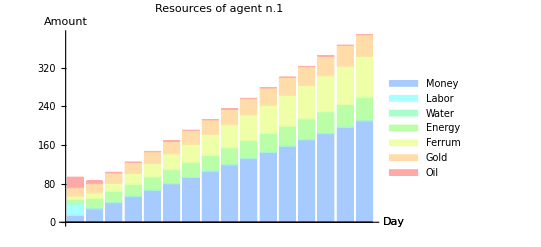

```mathematica
MAEVisProducts[1]
```

```mathematica
m = {{1, 2}};
n = {m};
n
```

{{{1,2}}}

```mathematica
n[[1]]
```

{{1,2}}

```mathematica
a = {{{1, 2}, {}}, {}, {{1}, {2}}};
Column@a
While[Length@a[[2]] < 3,AppendTo[a[[2]], {}]];
Column@a
AppendTo[a[[2,3]], {{1,1,1,1}, {2,2,2}}];Column@a
```

{{1,2},{}}
{}
{{1},{2}}

{{1,2},{}}
{{},{},{}}
{{1},{2}}

{{1,2},{}}
{{},{},{{{1,1,1,1},{2,2,2}}}}
{{1},{2}}

```mathematica
f[x_] := Abs[x];
Gather [{1,-1,3, 2, -2},f[#1] == f[#2]&]
```

{{1,-1},{3},{2,-2}}

```mathematica
f[{1,-2,3}]
```

{1,2,3}

```mathematica
ab = {1,2};
AddTo[ab,{30,40}];
ab
ab += {-1, -2};
ab
```

{31,42}

{30,40}

```mathematica
mn = 3;
an = 5;
dls = ({0, 0} &/@ Range@an) &/@ Range@mn
```

{{{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}},{{0,0},{0,0},{0,0},{0,0},{0,0}}}

```mathematica
qq = {1,2,3};
qq[[-1]] = 2;
qq
```

```mathematica
{1,2,2}

RandomReal[{5,6}]
```

{1,2,2}

```mathematica
qq = {{{}, {}}, {}, {}}; 
qq[[1]]
Length@qq[[3]]
AppendTo[qq[[1,2]], 55];
qq
```

{{},{}}

0

```mathematica
qq = {{{},{55, 56}},{},{}}
Last@Last@qq[[1]]
```

{{{},{55,56}},{},{}}

56

```mathematica
ff[a_, b_] := a+b;
ar = {{1,2},{2,3}};
ff /@ ar
```

{ff[{1,2}],ff[{2,3}]}

```mathematica
w = {1,2,3,4};
w[[-2]]
```

3

```mathematica
f[x_] := Abs[x];
ar = {1,2,3};
f[ar]
Abs[{1,2,3}]
```

{1,2,3}

{1,2,3}

```mathematica
l = Gather[{{2,3,4}}, #1 == #2&]
l[[1]]
```

{{{2,3,4}}}

{{2,3,4}}

```mathematica
Accumulate [{{1,2}, {1,3}, {1,4}}]
```

{{1,2},{2,5},{3,9}}

{{1,10},{2,20},{3,30}}

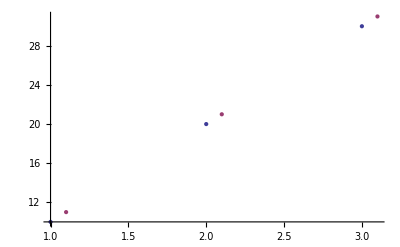

```mathematica
aq = {1,2,3};
ap = {10, 20, 30};
bq = {1.1, 2.1, 3.1};
bp = {11, 21, 31};
MapThread[List,{aq,ap}]

ListPlot[{x,y}]
```

```mathematica
1
```

```mathematica
Flatten[Outer[List, {1,2},{3,4,5}], 1]
Map[Flatten, Outer[List, {1,2},{3,4}] , {2}]
```

{{1,3},{1,4},{1,5},{2,3},{2,4},{2,5}}

{{{1,3},{1,4}},{{2,3},{2,4}}}

```mathematica
Dimensions[{{{1,3},{1,4}},{{2,3},{2,4}}}]
```

{2,2,2}

```mathematica
SortBy[{3,4,21,6,3,2,1},-Abs[#]&]
```

{21,6,4,3,3,2,1}

```mathematica
Module[{func, x,y,temp,asks,bids,s,f},

func := (temp={};
Print[#];
For[i=1,i≤Length@#[[1]],i++,
s=If[i==1,0,#[[1,i-1]]];
f=#[[1, i]];
AppendTo[temp,{#[[2,i]],ToExpression["x > "<>ToString@s<>" && "<>"x <= "<>ToString@f]}];
];
temp)&;
func /@ {{{1,2},{10,20}}, {{2,3},{11,21}}}
]
```

{{1,2},{10,20}}

{{2,3},{11,21}}

{{{10,x>0&&x≤1},{20,x>1&&x≤2}},{{11,x>0&&x≤2},{21,x>2&&x≤3}}}

```mathematica
out = {};
nums = {{1}, {2}, {3}};
Function[num,
	AppendTo[out, num[[1]]];
] /@ nums;
out
Head[out]
```

{1,2,3}

List

```mathematica
bl = 3 < 4;
bl
```

True

```mathematica
cc = {0.4, 0.6};
RandomReal[cc]
```

0.541779

```mathematica
ListPlot[{{"1/1", 2}, {"1/2", 3}}]
```

-Graphics-

```mathematica
a = {1,2,3}
a /. x_  /; x==2 -> 4
a
```

{1,2,3}

{1,4,3}

{1,2,3}

```mathematica
p = day->3;
Last@p
```

3

```mathematica
Flatten[hMarketsBooks[[1,1,1,All]], 1]
```

{{8.33383,5.25202,Ask,5,9},{2.66257,5.9976,Bid,2,4},{7.12264,5.63382,Bid,3,6},{4.12992,5.71642,Bid,6,13}}

```mathematica
Grid[{{"a", "b", "c"}, {Column@{"a", "b"}, "c", "v"}}]
```

a | b | c
a
b | c | v

```mathematica
First@First@Position[{1,2,3}, 1]
```

1